# Vaja 7

1. naloga

```mathematica
SetDirectory[NotebookDirectory[]]
```

U:\ROM\ROM\Vaja7

```mathematica
rez =Import["rezultati.xlsx"]//First
```

{{Priimek,Ime,Skupina,Točke},{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
rez//TableForm
```

Priimek | Ime | Skupina | Točke
Furlan | Luka | A | 93.
Karakaš | Alenka | A | 94.
Kočar | Petra | B | 44.
Kofol | Andraž | C | 34.
Kumar | Barbara | B | 67.
Logar | Mateja | A | 42.
Pance | Martin | B | 64.
Pleterski | Vesna | C | 30.
Trček | Valerija | B | 70.
Virant | Primož | C | 58.
Vesel | Polona | C | 66.
Žveglič | Katarina | A | 46.
Cvelbar | Janja | B | 39.
Furlan | Aleš | B | 36.
Iskra | Sabina | A | 77.
Jerman | Katja | B | 100.
Karničar | Jaka | C | 26.
Korošec | Kristina | B | 86.
Kržišnik | Grega | B | 90.
Obrenović | Tatjana | C | 44.
Puncer | Primož | A | 57.
Ribnikar | Matjaž | A | 43.
Štemberger | Igor | B | 85.
Šubašič | Matej | C | 76.
Tekavčič | Aleksander | A | 34.
Tratnik | Mojca | B | 79.
Smrekar | Andreja | A | 38.
Bezek | Tomaž | B | 38.

2. naloga

```mathematica
Imena[podatki_]:= First[podatki]
```

```mathematica
Imena[rez]
```

{Priimek,Ime,Skupina,Točke}

```mathematica
Podatki[podatki_]:= Rest[podatki]
```

```mathematica
Podatki[rez]
```

{{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
IndeksStolpca[podatki_,stolpec_]:= Module[{polozaj},
polozaj=Position[Imena[podatki],stolpec]; 
If[ polozaj== {},Null,polozaj[[1,1]]]
]
```

```mathematica
IndeksStolpca[rez,"Ime"]
```

2

```mathematica
Stolpec[podatki_,stolpec_]:= Module[{spremenjeni,polozajStolpca},
spremenjeni = Transpose[Podatki[podatki]];
polozajStolpca = IndeksStolpca[podatki,stolpec];
spremenjeni[[polozajStolpca]]
]
```

```mathematica
Stolpec[rez,"Ime"]
```

{Luka,Alenka,Petra,Andraž,Barbara,Mateja,Martin,Vesna,Valerija,Primož,Polona,Katarina,Janja,Aleš,Sabina,Katja,Jaka,Kristina,Grega,Tatjana,Primož,Matjaž,Igor,Matej,Aleksander,Mojca,Andreja,Tomaž}

```mathematica
Stolpec[rez,"Skupina"]
```

{A,A,B,C,B,A,B,C,B,C,C,A,B,B,A,B,C,B,B,C,A,A,B,C,A,B,A,B}

```mathematica
PovprecjeTock[podatki_] := Mean[Stolpec[podatki,"Točke"]]
```

```mathematica
PovprecjeTock[rez]
```

59.1429

```mathematica
RazlicneVrednosti[podatki_,stolpec_] := Union[Stolpec[podatki,stolpec]]
```

```mathematica
RazlicneVrednosti[rez,"Skupina"]
```

{A,B,C}

```mathematica
Vrstica[podatki_,i_]:= Podatki[podatki][[i]]
```

```mathematica
Vrstica[rez,1]
```

{Furlan,Luka,A,93.}

```mathematica
Vrstica[rez,3]
```

{Kočar,Petra,B,44.}

3. naloga

```mathematica
meje ={50,60,70,80,90}
```

{50,60,70,80,90}

```mathematica
OcenaZaMeje[{za6_,za7_,za8_,za9_,za10_},tocke_]:=Module[{},
If[tocke ≥ za10,Return[10]];
If[tocke ≥ za9,Return[9]];
If[tocke ≥ za8,Return[8]];
If[tocke ≥ za7,Return[7]];
If[tocke ≥ za6,Return[6]];
0
]
```

```mathematica
OcenaZaMeje[meje,89]
```

9

```mathematica
OcenaZaMeje[meje,45]
```

0

```mathematica
Ocene[podatki_,meje_]:= Module[{Kriterij},
Kriterij[tocke_]:=OcenaZaMeje[meje,tocke];
Map[Kriterij,Stolpec[podatki,"Točke"]]
]
```

```mathematica
Ocene[rez, meje]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

```mathematica
DodajStolpec[podatki_,ime_,podStolpec_]:=Transpose[Append[Transpose[podatki],Prepend[podStolpec,ime]]]
```

```mathematica
noviPodatki = DodajStolpec[rez, "Ocene", Ocene[rez, meje]] // TableForm
```

Priimek | Ime | Skupina | Točke | Ocene
Furlan | Luka | A | 93. | 10
Karakaš | Alenka | A | 94. | 10
Kočar | Petra | B | 44. | 0
Kofol | Andraž | C | 34. | 0
Kumar | Barbara | B | 67. | 7
Logar | Mateja | A | 42. | 0
Pance | Martin | B | 64. | 7
Pleterski | Vesna | C | 30. | 0
Trček | Valerija | B | 70. | 8
Virant | Primož | C | 58. | 6
Vesel | Polona | C | 66. | 7
Žveglič | Katarina | A | 46. | 0
Cvelbar | Janja | B | 39. | 0
Furlan | Aleš | B | 36. | 0
Iskra | Sabina | A | 77. | 8
Jerman | Katja | B | 100. | 10
Karničar | Jaka | C | 26. | 0
Korošec | Kristina | B | 86. | 9
Kržišnik | Grega | B | 90. | 10
Obrenović | Tatjana | C | 44. | 0
Puncer | Primož | A | 57. | 6
Ribnikar | Matjaž | A | 43. | 0
Štemberger | Igor | B | 85. | 9
Šubašič | Matej | C | 76. | 8
Tekavčič | Aleksander | A | 34. | 0
Tratnik | Mojca | B | 79. | 8
Smrekar | Andreja | A | 38. | 0
Bezek | Tomaž | B | 38. | 0

```mathematica
Export["ocene.xlsx",noviPodatki]
```

ocene.xlsx

```mathematica
podatkiOcene =DodajStolpec[rez, "Ocene", Ocene[rez, meje]]
```

{{Priimek,Ime,Skupina,Točke,Ocene},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Kočar,Petra,B,44.,0},{Kofol,Andraž,C,34.,0},{Kumar,Barbara,B,67.,7},{Logar,Mateja,A,42.,0},{Pance,Martin,B,64.,7},{Pleterski,Vesna,C,30.,0},{Trček,Valerija,B,70.,8},{Virant,Primož,C,58.,6},{Vesel,Polona,C,66.,7},{Žveglič,Katarina,A,46.,0},{Cvelbar,Janja,B,39.,0},{Furlan,Aleš,B,36.,0},{Iskra,Sabina,A,77.,8},{Jerman,Katja,B,100.,10},{Karničar,Jaka,C,26.,0},{Korošec,Kristina,B,86.,9},{Kržišnik,Grega,B,90.,10},{Obrenović,Tatjana,C,44.,0},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Štemberger,Igor,B,85.,9},{Šubašič,Matej,C,76.,8},{Tekavčič,Aleksander,A,34.,0},{Tratnik,Mojca,B,79.,8},{Smrekar,Andreja,A,38.,0},{Bezek,Tomaž,B,38.,0}}

5. naloga

```mathematica
steviloOcen = Drop[Rest[BinCounts[Ocene[rez,meje]]],{2,6}]
```

{13,2,3,4,2,4}

6. naloga

```mathematica
oznakeHorizontalneOsi = {"Negativno",6,7,8,9,10}
```

{Negativno,6,7,8,9,10}

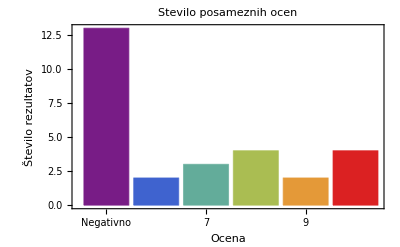

```mathematica
BarChart[steviloOcen,ChartStyle->"Rainbow",ChartLabels->oznakeHorizontalneOsi,FrameLabel-> {"Ocena","Število rezultatov"},Frame->True,PlotLabel->"Stevilo posameznih ocen"]
```

7. naloga

```mathematica
Zaokrozi[x_]:= ToString[DecimalForm[x,{3,1}]]
```

```mathematica
delezi = Map[Zaokrozi,N[steviloOcen/Apply[Plus,steviloOcen]]*100]
```

{46.4,7.1,10.7,14.3,7.1,14.3}

```mathematica
Zdruzi[napis_,delez_]:=StringJoin[ToString[napis]," (",delez,"%)"]
```

```mathematica
oznakeZOdstotki = MapThread[Zdruzi,{steviloOcen,delezi}]
```

{13 (46.4%),2 (7.1%),3 (10.7%),4 (14.3%),2 (7.1%),4 (14.3%)}

```mathematica
PieChart3D[steviloOcen,ChartLabels-> oznakeZOdstotki,ChartStyle-> "Rainbow"]
```

-Graphics3D-

8. naloga

```mathematica
UstrezaPogoju[podatki_,vrstica_,stolpec_,primerjava_,vrednost_]:=Module[{inxStolpca,element},
inxStolpca = IndeksStolpca[podatki,stolpec];
element = vrstica[[inxStolpca]];
primerjava[element,vrednost]
]
```

```mathematica
v1=Vrstica[podatkiOcene,2]
v2=Vrstica[podatkiOcene,3]
```

{Karakaš,Alenka,A,94.,10}

{Kočar,Petra,B,44.,0}

```mathematica
UstrezaPogoju[podatkiOcene,v1,"Ocene",Equal,10]
```

True

9. naloga

```mathematica
IzberiVrstice[podatki_,stolpec_,primerjava_,vrednost_]:=Module[{vrstice,izberi},
vrstice := Podatki[podatki];
izberi[v_]:=UstrezaPogoju[podatki,v,stolpec,primerjava,vrednost];
Insert[Select[vrstice,izberi],Imena[podatki],1]
]
```

```mathematica
IzberiVrstice[podatkiOcene,"Ocene",Equal,10]
```

{{Priimek,Ime,Skupina,Točke,Ocene},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Jerman,Katja,B,100.,10},{Kržišnik,Grega,B,90.,10}}

```mathematica
IzberiVrstice[podatkiOcene,"Skupina",Equal,"A"]
```

{{Priimek,Ime,Skupina,Točke,Ocene},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Logar,Mateja,A,42.,0},{Žveglič,Katarina,A,46.,0},{Iskra,Sabina,A,77.,8},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Tekavčič,Aleksander,A,34.,0},{Smrekar,Andreja,A,38.,0}}